Visualizing the kinematics of relativistic wave packets

Bernd Thaller, arXiv:quant-ph/0409079v1 (2004)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

## Example 1

```mathematica
Clear[h0,m,c,p,λ,k,ψhat0,ϕposk,ϕnegk,int,t,ρ,kdim,kmax,dk,ψx1,ψx2,ψk1,ψk2,ψ,ψ1,ψ2]
ψ[t,x]={ψ1[t,x],ψ2[t,x]}
D[ψ[t,x],t]
(-I PauliMatrix[1].D[ψ[t,x],x]+PauliMatrix[3].ψ[t,x])/I//Expand
```

{ψ1[t,x],ψ2[t,x]}

{ψ1^(1,0)[t,x],ψ2^(1,0)[t,x]}

{-ⅈ ψ1[t,x]-ψ2^(0,1)[t,x],ⅈ ψ2[t,x]-ψ1^(0,1)[t,x]}

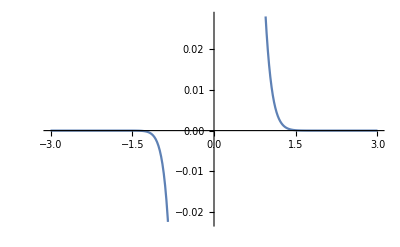

```mathematica
Clear[h0,m,c,p,λ,k,ψhat0,ϕposk,ϕnegk,int,t,ρ,kdim,kmax,dk,ψx1,ψx2,ψk1,ψk2,upospxt,unegpxt,unegp,uposp,ψ0,ψ0hat,ψposhat,ψneghat,integrand,ψ13,ρ,xmax,xdim,pmax,tab0]
xmax=20;
xdim=21;
pmax=4;

(* natural units *)
m=c=ℏ=1;

(* equation7: free Dirac hamiltonian *)
h0={{m c^2,c p},{c p,-m c^2}};
(* eigenvalue *)
λ=Eigenvalues[h0][[2]];
(* eigenvectos *)
{unegp,uposp}=Eigenvectors[h0]//Simplify;

(* check equation 9 *)
h0.uposp-λ uposp//Simplify;
h0.unegp+λ unegp//Simplify;

(* equation 8: build plane wave solutions *)
upospxt=1/Sqrt[2π] uposp Exp[I p x-I λ t];
unegpxt=1/Sqrt[2π] unegp Exp[I p x+I λ t];

(*** example 1 ***)
(* equation 15: initial wave packet *)
ψ0=(1/(32π))^(1/4)Exp[-x^2/16]{1,1};
(* equation 16: Fourier transform *)
ψ0hat=FourierTransform[ψ0,x,p];

(* equation 14: Fourier coefficient functions *)
ψposhat=(1/2(IdentityMatrix[2]+h0/λ).ψ0hat//Simplify)[[1]];
ψneghat=(1/2(IdentityMatrix[2]-h0/λ).ψ0hat//Simplify)[[2]];

integrand=ψposhat upospxt+ψneghat unegpxt;

(* singularity at p=0 *)
Plot[Re[integrand[[1]]]/.{t->0,x->0},{p,-3,3},PlotRange->Automatic,PlotPoints->5,Exclusions->{0}]
```

## Example 2

```mathematica
Clear[h0,m,c,p,λ,k,ψhat0,ϕposk,ϕnegk,int,t,ρ,kdim,kmax,dk,ψx1,ψx2,ψk1,ψk2,ψ,ψ1,ψ2]

(* natural units *)
m=c=ℏ=1;

(* equation7: free Dirac hamiltonian *)
h0={{m c^2,c p},{c p,-m c^2}};
(* eigenvalue *)
λ=Eigenvalues[h0][[2]];
(* eigenvectos *)
{unegp,uposp}=Eigenvectors[h0]//Simplify;

(*** example 2 ***)
(* equation 17: initial wave packet *)
ψ0=(1/(32π))^(1/4)Exp[-x^2/16-I 3x/4]{1,1};
(* Fourier transform *)
ψ0hat=FourierTransform[ψ0,x,p]

(* equation 14: Fourier coefficient functions *)
ψposhat=(1/2(IdentityMatrix[2]+h0/λ).ψ0hat//Simplify)[[1]]
ψneghat=(1/2(IdentityMatrix[2]-h0/λ).ψ0hat//Simplify)[[2]]
```

{ⅇ^(-1/4 (3-4 p)^2) (2/π)^(1/4),ⅇ^(-1/4 (3-4 p)^2) (2/π)^(1/4)}

(ⅇ^(-1/4 (3-4 p)^2) (1+p+√(1+p^2)))/(2^(3/4) √(1+p^2) π^(1/4))

(ⅇ^(-1/4 (3-4 p)^2) (1-p+√(1+p^2)))/(2^(3/4) √(1+p^2) π^(1/4))

## Example 3

```mathematica
Clear[h0,m,c,p,λ,k,ψhat0,ϕposk,ϕnegk,int,t,ρ,kdim,kmax,dk,ψx1,ψx2,ψk1,ψk2,ψ,ψ1,ψ2]

(*** example 3 ***)
(* equation 23: initial wave packet *)
ψ0=(1/(4π))^(1/4)Exp[-x^2/8]{1,0};
(* Fourier transform *)
ψ0hat=FourierTransform[ψ0,x,p]

(* equation 14: Fourier coefficient functions *)
ψposhat=(1/2(IdentityMatrix[2]+h0/λ).ψ0hat//Simplify)[[1]]
ψneghat=(1/2(IdentityMatrix[2]-h0/λ).ψ0hat//Simplify)[[2]]
```

{(√2 ⅇ^(-2 p^2))/π^(1/4),0}

(ⅇ^(-2 p^2) (h0+λ))/(√2 π^(1/4) λ)

-(ⅇ^(-2 p^2) h0)/(√2 π^(1/4) λ)